# Computing for Mathematical Physics

## Exercises 2: Lists

```mathematica
Clear["Global`*"]
```

Click on the line above and press ⇧+⌤ to restart the exercises with any previously held definitions cleared from the memory.

Alternatively, one can restart the Mathematica kernel, which has the same effect, by selecting Evaluation→Quit Kernel→Local from the drop-down menu. Another way to quit the kernel is to type Quit[] in an input cell and then evaluate it by pressing ⇧+⌤.

You are encouraged to use Mathematica's built-in help in the course of these exercises.

## Tips

Mathematica is case sensitive. 

For example, should you define a variable matrix in your code, you must refer to/access it by typing matrix rather than, e.g. Matrix. If you try to refer to, or access, matrix by typing Matrix you will either be accessing something which is completely undefined, or other than what you meant to access.

Mathematica’s internal functions all start with capital letters.

To help distinguish your code and variables from those internal to Mathematica we therefore recommend starting all user-defined variable and function names with a lowercase letter.

All functions in Mathematica, both internal and user-defined, have their arguments enclosed in single square brackets, e.g. Sin[x], Cos[x], Plot[...], etc.

Round brackets are instead reserved for the usual bracketing of operations, indicating an evaluation order for the various components of an expression, e.g. 2(x+4+Sin[x])^2+Cos[y], etc.

It is good practice to use variables names which are both intuitive and meaningful. If variable names end up comprising of more than one word or abbreviation, we maintain readability by using either camelCase or  snake case.

camelCase variables have words/abbreviations distinguished form one another by capitals, e.g. someVariable.

snake case variables have words/abbreviations separated by a letter space entered as  Esc _ Esc , e.g. some variable.

N.B. In Mathematica a letter space is not the same as a regular underscore. A regular underscore is simply entered as _. A letter space is entered as  Esc _ Esc . Regular underscores have a particularly special meaning in Mathematica, as we shall see in the coming classes, and so they cannot be used within variable names: only letter space can be used in that context ( Esc _ Esc ).

If distinguishing between letter spaces and regular underscores seems too much to take in, please keep things simple and just adopt camelCase.

## Handy Keyboard Shortcuts

In the longer term, you will certainly find it more efficient to learn at least a few very useful keyboard short-cuts, to avoid having to use the mouse and palettes. Short-cuts for superscript, square-root, pi, ⅇ, and ∞ are especially useful (next subsection).

The material in the subsections below is purely intended as a help, and it contains no questions.

### Frequently used mathematical notation

To use the palette and mouse to enter things like superscripts, integrals, etc, go to the drop-down menu at the top of the screen and select Palettes → Basic Math Assistant .

While it's fine to use the palettes to help enter expressions, particularly on meeting Mathematica for the first time(s), many people find it much more useful and faster in the long-run to be able to enter everything from the keyboard, without any need to go to the mouse.

Some frequently used quick keyboard formulations are shown in the grey box below.
These are generally quite intuitive, and require only a very small investment of time to become fluent in; this pays dividends.

-Graphics-

[Copied from https://reference.wolfram.com/language/tutorial/MathematicalAndOtherNotation.html .]

### Switching from input cells to other cell format types, e.g. text cells

Changing the style of a cell (Input/Text) can be done via the drop-down menu at the top of the screen: Format → Style → Input/Text.

Note that Mathematica only interprets the contents of input cells as code to be processed and run. The contents of text cells is not interpreted as code by Mathematica, and is therefore left as-is. (Aside: one should be careful therefore, when entering code, to be clear that the cell you are working with is indeed an input cell and not a text cell. If in doubt, clicking Format → Style and looking for the ✓ will reveal the currently selected cell’s format type.)

By default, all new cells are input cells. However, writing text cells is essential for communicating the purpose and meaning of code appearing in the input cells to the reader.

Alternatively, the next grey box below shows handy short-key entries for quickly changing the cell style format directly from the keyboard, avoiding the mouse: Alt+7 is especially useful, as it enables us to write text cells like this one, which one will do somewhat frequently later in this course.

Note, on a Mac, you would need to swap the Alt buttons below for ⌘.

-Graphics-

These and further keyboard shortcuts can be found here https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html .

### Greek letters

Entering Greek letters couldn’t really be more easy.
Typically, you just type Esc, then the first letter in the name of the Greek letter you want to print, then Esc again:

-Graphics-
See here for further details: https://reference.wolfram.com/language/tutorial/InputAndOutputInNotebooks.html#14875 .

### Less frequently used mathematical notation

One would typically tend to write the relevant long-hand Mathematica command instead of using the keyboard escape sequences below, for integrals etc.

This is often because, at least in the case of integrals and sums, one often needs to provide Mathematica some helpful assumptions about the nature of parameters appearing in the integrand (real / imaginary / positive / negative / bigger-than-some-other-parameter / ... etc) in order for it to proceed to a meaningful answer.

We only really point these out below as they are fairly intuitive too, despite the caveat above.

## Introduction to lists in Mathematica

### Data for use in the questions

• The exercises make use of the following lists.
• Execute the following cell with ⇧+⌤ before attempting the questions.
• Do not edit the data below in any way.

```mathematica
(* Q1 *)
matrix={
{r,s,t},
{u,v,w},
{x,y,z}};

(* Q1 *)
vector={I,π,E};

(* Q2 *)
coinTypes={1,2,5,10,20,50,100};

(* Q3 *)
names={
{"Juan","Maldacena"},
{"Ed","Witten"},
{"Emmy","Noether"},
{"Srinivasa","Ramanujan"},
{"James","Gates"},
{"Fabiola","Gianotti"},
{"Stefano","Catani"}};

(* Q4 *)
piDigits=RealDigits[N[Pi,1000]][[1]];
```

### 1. Accessing matrices and vectors, matrix-vector multiplication, and transposition.

In this question we will perform various operations on the matrix matrix and the vector vector defined in the section above titled Data used within the questions.

a) Extract the second row of matrix.

```mathematica
Take[matrix, {2}]
```

{{u,v,w}}

b) Extract the second column of matrix, using Transpose.

```mathematica
Take[Transpose[matrix], {2}]
```

{{s,v,y}}

c) Take the matrix product of matrix with vector.

```mathematica
matrix.vector
```

{ⅈ r+π s+ⅇ t,ⅈ u+π v+ⅇ w,ⅈ x+π y+ⅇ z}

d) Compute the scalar product vector.matrix.vector.

```mathematica
vector.matrix.vector
```

ⅈ (ⅈ r+π u+ⅇ x)+π (ⅈ s+π v+ⅇ y)+ⅇ (ⅈ t+π w+ⅇ z)

e) Confirm that vector.Transpose[matrix]= matrix.vector.

```mathematica
vectranspose =vector.Transpose[matrix]
vecdotprod = matrix.vector
vecdotprod== vectranspose
```

{ⅈ r+π s+ⅇ t,ⅈ u+π v+ⅇ w,ⅈ x+π y+ⅇ z}

{ⅈ r+π s+ⅇ t,ⅈ u+π v+ⅇ w,ⅈ x+π y+ⅇ z}

True

### 2. Combinatorics: summing one, two, and three coins.

The list coinTypes gives the values in pence of the coins in circulation in the UK up to a value of £1. 

In answering this question you might use Outer, Flatten, Union, Intersection, Complement, Count, and Table or Range.

a) How many different sums from zero up to and including £2 can be formed out of one or two or three coins? The coins in each sum do not all need to be different, but at least one coin must be used.

You may find breaking the task down into small simple steps helpful, e.g.,

• i)  Create the list of possible sums using just one coin : oneCoinPossibilities.

• ii) Use Outer[Plus, ...,...] to form all possible sums of exactly two coins in the coinTypes list: twoCoinPossibilities. Take care to flatten the resulting array and remove any duplicate elements. 

• iii) Use Outer[Plus, ...,...] again with the latter result and coinTypes to create a list of possible sums with exactly three coins: threeCoinPossibilities.

• iv) Consider combining the results of i), ii) and iii) to obtain the list of all possible different sums from zero up to and including £2.

```mathematica
oneCoinPossibilities = coinTypes
```

{1,2,5,10,20,50,100}

```mathematica
twoCoinAllPossibilities =Flatten[Outer[Plus, oneCoinPossibilities,oneCoinPossibilities]]
twoCoinPossibilities = Union[twoCoinAllPossibilities,twoCoinAllPossibilities]
threeCoinAllPossibilities = Flatten[Outer[Plus, oneCoinPossibilities,twoCoinPossibilities]]
threeCoinPossibilities = Union[threeCoinAllPossibilities,threeCoinAllPossibilities]
AllthreeCoinPossibilities = Union[oneCoinPossibilities,twoCoinPossibilities, threeCoinPossibilities]
```

{2,3,6,11,21,51,101,3,4,7,12,22,52,102,6,7,10,15,25,55,105,11,12,15,20,30,60,110,21,22,25,30,40,70,120,51,52,55,60,70,100,150,101,102,105,110,120,150,200}

{2,3,4,6,7,10,11,12,15,20,21,22,25,30,40,51,52,55,60,70,100,101,102,105,110,120,150,200}

{3,4,5,7,8,11,12,13,16,21,22,23,26,31,41,52,53,56,61,71,101,102,103,106,111,121,151,201,4,5,6,8,9,12,13,14,17,22,23,24,27,32,42,53,54,57,62,72,102,103,104,107,112,122,152,202,7,8,9,11,12,15,16,17,20,25,26,27,30,35,45,56,57,60,65,75,105,106,107,110,115,125,155,205,12,13,14,16,17,20,21,22,25,30,31,32,35,40,50,61,62,65,70,80,110,111,112,115,120,130,160,210,22,23,24,26,27,30,31,32,35,40,41,42,45,50,60,71,72,75,80,90,120,121,122,125,130,140,170,220,52,53,54,56,57,60,61,62,65,70,71,72,75,80,90,101,102,105,110,120,150,151,152,155,160,170,200,250,102,103,104,106,107,110,111,112,115,120,121,122,125,130,140,151,152,155,160,170,200,201,202,205,210,220,250,300}

{3,4,5,6,7,8,9,11,12,13,14,15,16,17,20,21,22,23,24,25,26,27,30,31,32,35,40,41,42,45,50,52,53,54,56,57,60,61,62,65,70,71,72,75,80,90,101,102,103,104,105,106,107,110,111,112,115,120,121,122,125,130,140,150,151,152,155,160,170,200,201,202,205,210,220,250,300}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,20,21,22,23,24,25,26,27,30,31,32,35,40,41,42,45,50,51,52,53,54,55,56,57,60,61,62,65,70,71,72,75,80,90,100,101,102,103,104,105,106,107,110,111,112,115,120,121,122,125,130,140,150,151,152,155,160,170,200,201,202,205,210,220,250,300}

```mathematica
possiblevalues = Intersection[Range[1,200],AllthreeCoinPossibilities]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,20,21,22,23,24,25,26,27,30,31,32,35,40,41,42,45,50,51,52,53,54,55,56,57,60,61,62,65,70,71,72,75,80,90,100,101,102,103,104,105,106,107,110,111,112,115,120,121,122,125,130,140,150,151,152,155,160,170,200}

b) Form the list of values from zero up to and including £2 that cannot be made up in this way. How many are there?

```mathematica
impossiblevalues = Complement[Range[0,200], possiblevalues]
```

{0,18,19,28,29,33,34,36,37,38,39,43,44,46,47,48,49,58,59,63,64,66,67,68,69,73,74,76,77,78,79,81,82,83,84,85,86,87,88,89,91,92,93,94,95,96,97,98,99,108,109,113,114,116,117,118,119,123,124,126,127,128,129,131,132,133,134,135,136,137,138,139,141,142,143,144,145,146,147,148,149,153,154,156,157,158,159,161,162,163,164,165,166,167,168,169,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199}

c) What is the smallest and what is the largest in the range that cannot be made?

```mathematica
First[impossiblevalues]
Last[impossiblevalues]
```

0

199

d) Check that the sum of the number that can be made and the number that cannot is 201.

```mathematica
Length[Join[impossiblevalues, possiblevalues]]
```

201

### 3. Sorting and shuffling lists.

Sort the list names into alphabetical order of second names. Do this by using the RotateLeft and/or RotateRight functions as well as Sort, and one or two other functions you find necessary. You may also use Transpose but the neatest solutions here avoid it.

```mathematica
surnamefirst =RotateLeft[names, {0,1}]
sortedsurname =Sort[surnamefirst]
names = RotateRight[sortedsurname, {0,1}]
```

{{Maldacena,Juan},{Witten,Ed},{Noether,Emmy},{Ramanujan,Srinivasa},{Gates,James},{Gianotti,Fabiola},{Catani,Stefano}}

{{Catani,Stefano},{Gates,James},{Gianotti,Fabiola},{Maldacena,Juan},{Noether,Emmy},{Ramanujan,Srinivasa},{Witten,Ed}}

{{Stefano,Catani},{James,Gates},{Fabiola,Gianotti},{Juan,Maldacena},{Emmy,Noether},{Srinivasa,Ramanujan},{Ed,Witten}}

### 4. Frequencies of list elements.

The list piDigits contains the first thousand digits in the decimal representation of π. Generate a table giving the frequencies of the digits 0 to 9 in that list. Check that the total of the frequencies is 1000.

```mathematica
frequency =Table[Count[piDigits, i], {i,0,9}]
TotalFrequency = Sum[frequency[[i]], {i,1,10}]
```

{93,116,103,103,93,97,94,95,100,106}

1000

### 5. More on frequencies of list elements: counting prime numbers.

Generate a table of 1000 random integers in the range 1 to 1000 (use the Help file on Random if necessary).

```mathematica
randomintegers =Table[RandomInteger[{1,1000},1000]]
```

{597,408,357,591,512,833,908,308,439,113,134,910,485,427,926,321,307,843,649,774,58,340,956,300,449,234,59,992,839,256,983,747,118,275,180,107,624,445,555,534,964,469,822,414,711,845,589,410,430,924,323,130,888,454,81,660,234,53,477,186,936,506,281,502,293,306,378,900,754,60,701,865,311,595,907,289,348,260,49,530,604,285,516,990,571,847,208,133,126,785,308,235,148,154,136,485,15,359,642,367,324,204,898,390,917,846,265,312,747,587,441,465,566,529,363,65,889,520,655,777,600,362,984,302,918,906,654,1000,732,76,21,408,644,386,170,755,699,357,897,997,352,623,211,335,953,284,128,183,934,224,897,656,77,370,795,58,708,486,603,776,97,387,675,157,302,786,962,719,395,331,657,210,921,107,957,124,866,127,210,526,239,921,538,896,56,336,559,896,373,664,135,536,10,962,646,937,553,37,734,683,462,991,481,606,467,693,126,23,245,733,265,941,167,406,925,883,447,452,787,397,276,147,502,846,39,271,993,347,604,535,93,551,36,979,563,300,105,536,204,662,6,372,264,567,496,869,246,137,275,980,162,651,578,17,165,487,433,60,851,227,801,253,358,561,618,600,359,899,301,847,456,858,375,775,333,117,76,709,5,78,438,242,302,949,77,141,539,148,44,363,341,841,535,653,963,813,443,989,598,322,579,271,272,560,815,455,550,510,711,305,26,128,148,658,178,151,793,610,383,282,69,545,304,902,415,789,252,446,215,245,962,783,966,385,488,920,640,245,291,179,499,699,803,775,371,218,463,277,838,765,573,769,551,985,573,953,548,276,647,733,905,177,8,167,891,485,310,386,911,504,482,803,356,337,597,771,143,274,828,17,468,451,261,264,155,463,395,30,278,44,949,348,640,722,886,12,884,482,914,67,270,176,415,556,530,382,830,438,56,179,610,51,799,741,598,912,725,256,640,513,878,714,499,303,246,213,597,819,29,191,227,136,647,714,119,121,956,30,656,247,769,487,241,206,587,115,344,201,777,857,122,446,101,330,763,141,221,623,883,838,868,44,756,284,826,430,158,992,693,98,534,806,258,600,981,869,299,30,186,940,918,732,725,634,799,444,378,210,645,841,602,322,267,106,519,637,165,313,77,855,256,934,366,997,406,98,723,402,921,465,780,668,508,801,907,765,733,948,416,126,488,329,222,410,453,319,344,962,504,82,769,658,25,283,608,914,834,520,958,64,670,296,25,780,712,15,151,873,275,520,540,665,509,15,576,813,503,452,862,299,145,866,41,604,436,312,55,81,606,675,645,531,902,127,399,204,724,6,623,650,939,867,731,794,987,207,606,987,825,836,526,243,435,954,575,901,437,57,838,212,392,673,603,946,681,907,558,330,995,785,35,245,217,844,969,215,618,111,217,38,25,751,191,799,597,485,53,143,165,269,632,877,610,682,421,739,871,474,712,670,536,974,12,672,80,227,657,839,387,208,930,206,834,530,245,706,599,269,577,21,353,271,656,468,615,950,641,705,499,992,984,91,581,109,33,907,402,161,793,274,81,424,233,241,454,93,623,309,823,857,818,256,259,397,819,120,700,40,865,218,294,205,212,94,505,402,343,665,193,102,604,40,10,394,926,600,45,798,764,730,210,399,893,349,526,833,836,938,292,770,389,860,950,402,710,707,308,101,600,465,254,424,758,501,723,341,146,512,821,840,834,130,281,230,720,627,840,205,329,742,669,273,319,191,996,967,607,278,375,853,401,359,204,676,282,607,557,866,739,969,47,529,231,487,17,998,251,881,990,408,162,955,338,818,431,405,221,51,602,57,9,963,954,843,886,17,18,359,335,645,222,690,853,607,445,727,86,5,173,863,218,565,149,952,104,137,359,957,452,1,660,533,861,366,69,212,76,907,828,502,898,443,367,363,745,107,633,278,814,229,246,890,363,766,90,75,598,12,530,277,933,289,165,436,987,928,932,711,356,308,179,653,699,465,433,150,871,930,312,581,600,898,82,172,835,135,192,663,239,650,988,926,913,1,664,296,830,272,467,897,29,636,510,509,7,864,454,133,839,245,655,155,677,369,62,909,706,38,122,733,416,44,546,461,785,138,884,601,690,52,160,168,827,411,549,221,654,771,474,144,499,576,810,531,512,348,942,704,160,318,429,680,241,745,878,147,579,537,556,88,855,28,844,517,349,746,499,240,681,254,129,661,411,320,74,836,207,518,829,880,299,474,390,946,326,474,21,923,621,479,367,329,399,975,490,474,976,178,956,531}

• i)    Select the prime numbers with the help of the PrimeQ function. How many are there?

```mathematica
primes =Select[randomintegers, PrimeQ]
```

{439,113,307,449,59,839,983,107,53,281,293,701,311,907,571,359,367,587,997,211,953,97,157,719,331,107,127,239,373,937,37,683,991,467,23,733,941,167,883,787,397,271,347,563,137,17,487,433,227,359,709,5,653,443,271,151,383,179,499,463,277,769,953,647,733,167,911,337,17,463,67,179,499,29,191,227,647,769,487,241,587,857,101,883,313,997,907,733,769,283,151,509,503,41,127,673,907,751,191,53,269,877,421,739,227,839,599,269,577,353,271,641,499,109,907,233,241,823,857,397,193,349,389,101,821,281,191,967,607,853,401,359,607,557,739,47,487,17,251,881,431,17,359,853,607,727,5,173,863,149,137,359,907,443,367,107,229,277,179,653,433,239,467,29,509,7,839,677,733,461,601,827,499,241,349,499,661,829,479,367}

• ii)   How many distinct prime numbers are there in the list?

```mathematica
distinctprimes = Union[primes]
```

{5,7,17,23,29,37,41,47,53,59,67,97,101,107,109,113,127,137,149,151,157,167,173,179,191,193,211,227,229,233,239,241,251,269,271,277,281,283,293,307,311,313,331,337,347,349,353,359,367,373,383,389,397,401,421,431,433,439,443,449,461,463,467,479,487,499,503,509,557,563,571,577,587,599,601,607,641,647,653,661,673,677,683,701,709,719,727,733,739,751,769,787,821,823,827,829,839,853,857,863,877,881,883,907,911,937,941,953,967,983,991,997}

• iii) Generate a list of the form
            { {1st prime number, number of associated occurrences in original list},
              {2nd prime number, number of associated occurrences in original list},
               ...
             {last prime number, number of associated occurrences in original list} }

Suppress the output by ending the command used to generate the full list with a semi-colon.
Instead, just display the first 10 elements of the list with <name of the list>[[1 ;; 10]] and the last 10 elements with <name of the list>[[-10 ;; -1]].

{{5},{7},{17},{23},{29},{37},{41},{47},{53},{59},{67},{97},{101},{107},{109},{113},{127},{137},{149},{151},{157},{167},{173},{179},{191},{193},{211},{227},{229},{233},{239},{241},{251},{269},{271},{277},{281},{283},{293},{307},{311},{313},{331},{337},{347},{349},{353},{359},{367},{373},{383},{389},{397},{401},{421},{431},{433},{439},{443},{449},{461},{463},{467},{479},{487},{499},{503},{509},{557},{563},{571},{577},{587},{599},{601},{607},{641},{647},{653},{661},{673},{677},{683},{701},{709},{719},{727},{733},{739},{751},{769},{787},{821},{823},{827},{829},{839},{853},{857},{863},{877},{881},{883},{907},{911},{937},{941},{953},{967},{983},{991},{997}}

0

### 6. How to time the execution of Mathematica evaluations.

The command Timing[<things to evaluate>;] will return an expression of the form, say, {0.003,Null}, where the 0.003 is the time taken to carry out  <things to evaluate>;, in seconds, and Null is the output of <things to evaluate>;.

Note that the return value, shown beside the time, is  Null due to the terminating semi-colon, ;, at the end of <things to evaluate>.  We want this semi-colon to be present, as Mathematica can sometimes take a substantial time figuring out how to actually display an expression on screen nicely, after it has already calculated it. If the task is particularly simple, but with a large output, the time taken for Mathematica to figure out how to display the object can be even longer than that taken to calculate it (which is what we are generally interested in).

i)  Use Table[...] to generate a list of the times taken to carry out the command Simplify[Expand[(a+b+c+d+e+f+8)^n] for n values between 1 and 12 (inclusive).

ii) Use ListPlot to plot the resulting times.

Note: Mathematica caches results it has obtained before. So, if you generate the table of timings a second time it will be much faster: Mathematica recognises that it already knows all the answers, and so it doesn’t actually compute anything the second/third/fourth time around. This is a really great feature of Mathematica, but for the purposes of this question, we are not interested in this caching ability, and we need to effectively disable it while we work here: this is done by inserting a function call, ClearSystemCache[], at the start of your solution here.

```mathematica
ClearSystemCache[]
```

{0.,0.,0.,0.,0.,0.03125,0.046875,0.0625,0.09375,0.171875,0.125,0.421875}

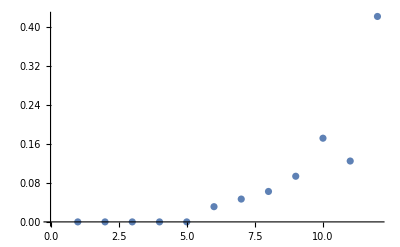

{{0.,Null},{0.,Null},{0.,Null},{0.,Null},{0.,Null},{0.,Null},{0.,Null},{0.015625,Null},{0.109375,Null},{0.140625,Null},{0.234375,Null},{0.375,Null}}

```mathematica
timingtable =Table[Timing[Simplify[Expand[(a+b+c+d+e+f+8)^n]];][[1]], {n,1,12}]
ListPlot[timingtable]
```

K. Hamilton, J. Bhamrah, J. Underwood, A.H. Harker — UCL
Last revision 14:30 25 Sep 2022